# MATH448 - Assignment 7 - 3/2/14

## Cameron Embree

```mathematica
countryByContinent=List[
List[CountryData["Africa"],Red],
List[CountryData["Asia"],Green],
List[CountryData["Europe"],LightBlue],
List[CountryData["NorthAmerica"],Blue],
List[CountryData["Oceania"],Pink],
List[CountryData["SouthAmerica"],Orange]
];

life=CountryData["Countries", "LifeExpectancy"];
gdp=CountryData["Countries", "GDPPerCapita"];
pop=CountryData["Countries", "Population"];
names=CountryData["Countries"];

gdpForCountry=DeleteCases[Partition[Riffle[gdp,names],2],{___,_Missing|_Missing,___}];

(* Retrives color for a country based on continent in countryByContinent *)
getColorByContinent[x_String]:=Select[countryByContinent,MemberQ[#[[1]],x]&][[1,2]]

(* Gets the name of a country based ona  provided gdp *)
getCountryByGDP[GDP_]:=Select[gdpForCountry,GDP==#[[1]]&][[1,2]]

(* Special ColorFunction method that given a GDP will find the country for the GDP and the color for the country based on it's continent *)
getColorForCountry[GDP_,LIFE_,POP_]:=getColorByContinent[getCountryByGDP[GDP]]


(*
(*TEST*)
gdpForCountry[[1]]
gdp[[1]]
names[[1]]

getCountryByGDP[gdp[[1]]]
getColorByContinent["Afghanistan"]
getColorByContinent[getCountryByGDP[gdp[[1]]]]
*)

dat=DeleteCases[Transpose[{gdp,life,pop}],{___,___,_Missing|___,_Missing,___|_Missing,___,___}];

BubbleChart[Tooltip[dat],FrameLabel->{"GDP", "Life Expectancy"},
ColorFunctionScaling->False,
ColorFunction->getColorForCountry
]
```

-Graphics-

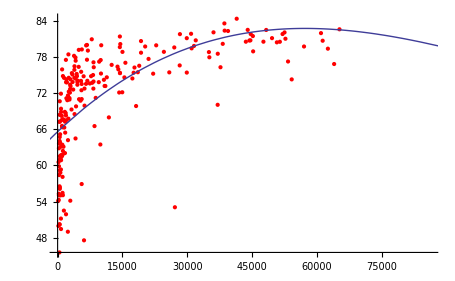

-Graphics-

```mathematica
(* Loading country data info *)
life=CountryData["Countries", "LifeExpectancy"];
gdp=CountryData["Countries", "GDPPerCapita"];
pop=CountryData["Countries", "Population"];

res=Transpose[{gdp,life,pop}];
trimmedDat=DeleteCases[res,{___,___,_Missing|___,_Missing,___|_Missing,___,___}];

(* Best fit of x-gdp to y-life *)
temp=Partition[Riffle[gdp,life],2];
temp=DeleteCases[temp,{___,_Missing|_Missing,___}];
fitLine=Fit[temp,{1,x,x^2,x^3},x];

(* TEST Basic graph of x-GDP to y-LIFE *)
Show[ListPlot[temp, PlotStyle->Red], Plot[fitLine, {x, -100000, 300000}]]


getColor[x1_,y1_,z1_]:=Block[{},
val=fitLine/.x->x1;
(*Print[" X: ",x1," Y: ",y1," Z: ",z1, " FUNC: ",fitLine, " ESTIMATED: ",val]*)
If[val>y1,Red,Blue]
]

Show[
BubbleChart[trimmedDat,
FrameLabel->{"GDP", "Life Expectancy"},
ColorFunctionScaling->False,
ColorFunction->getColor
],
Plot[fitLine,{x,0,300000}]
]
```

```mathematica
life=CountryData["Countries", "LifeExpectancy"];
gdp=CountryData["Countries", "GDPPerCapita"];
pop=CountryData["Countries", "Population"];


res=Transpose[{gdp,life,pop}];
trimmedDat=DeleteCases[res,{___,___,_Missing|___,_Missing,___|_Missing,___,___}];

(* Best fit of life *)
temp=Partition[Riffle[life,gdp],2];
temp=DeleteCases[temp,{___,_Missing|_Missing,___}];
fitLine=Fit[temp,{1,x,x^2,x^3,x^4},x]

getColor[x1_,y1_,z1_]:=Block[{},
val=fitLine/.x->y1;
(*Print[" X: ",x1," Y: ",y1," Z: ",z1, " FUNC: ",fitLine, " ESTIMATED: ",val];*)
If[val>x1,Red,Blue]
]
Plot[fitLine,{x,0,200000}]

Show[
BubbleChart[trimmedDat,
FrameLabel->{"GDP", "Life Expectancy"},
ColorFunctionScaling->False,
ColorFunction->getColor
],
Plot[fitLine,{x,0,200000}]
]
```

-968594.+50219.6 x-854.855 x^2+4.75076 x^3+0.00063402 x^4

-Graphics-

-Graphics-

```mathematica
(* Loading country data info *)
liter=CountryData["Countries", "LiteracyFraction"];
unemp=CountryData["Countries", "UnemploymentFraction"];
pop=CountryData["Countries", "Population"];

res=Transpose[{liter,unemp,pop}];
trimmedDat=DeleteCases[res,{___,___,_Missing|___,_Missing,___|_Missing,___,___}];

(* Best fit of x-gdp to y-life *)
temp=Partition[Riffle[liter,unemp],2];
temp=DeleteCases[temp,{___,_Missing|_Missing,___}];
fitLine=Fit[temp,{1,x,x^2,x^3},x];

getColor[x1_,y1_,z1_]:=Block[{},
val=fitLine/.x->x1;
If[val>y1,Red,Green]
]

Show[
BubbleChart[trimmedDat,
FrameLabel->{"Literacy Fraction", "Unemplyment Fraction"},
ColorFunctionScaling->False,
ColorFunction->getColor
],
Plot[fitLine,{x,0,2}]
]
```

-Graphics-